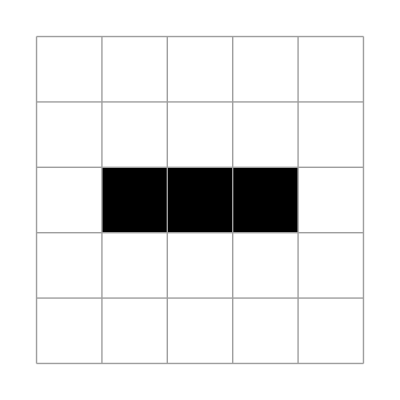

```mathematica
lr;
Clear[x,xp];
({{xp[1,1], xp[1,2], xp[1,3], xp[1,4], xp[1,5]}, {xp[2,1], xp[2,2], xp[2,3], xp[2,4], xp[2,5]}, {xp[3,1], xp[3,2], xp[3,3], xp[3,4], xp[3,5]}, {xp[4,1], xp[4,2], xp[4,3], xp[4,4], xp[4,5]}, {xp[5,1], xp[5,2], xp[5,3], xp[5,4], xp[5,5]}})=loob[({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}})];
aplt[xp]
```

```mathematica
lr
```

and::shdw: Symbol and appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

```mathematica
lr
```

```mathematica
<<life`;
bool[True]//loob
```

True

```mathematica
Clear[update,xp];
<<life`;
count[k_,{i_,j_}]:=BooleanCountingFunction[{k},Delete[Flatten[Array[x,{3,3},{i,j}-1]],5]];
xpArray2=({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
update[xpArray_]:=Module[
{formulaIJ,formula,varlist,out1}
,
({{xp[1,1], xp[1,2], xp[1,3], xp[1,4], xp[1,5]}, {xp[2,1], xp[2,2], xp[2,3], xp[2,4], xp[2,5]}, {xp[3,1], xp[3,2], xp[3,3], xp[3,4], xp[3,5]}, {xp[4,1], xp[4,2], xp[4,3], xp[4,4], xp[4,5]}, {xp[5,1], xp[5,2], xp[5,3], xp[5,4], xp[5,5]}})=loob[xpArray];
formulaIJ=(and@{Nothing,(x[##]&&count[{0},{##}])~Implies~!xp[##],(x[##]&&count[{1},{##}])~Implies~!xp[##],(x[##]&&count[{2},{##}])~Implies~xp[##],(x[##]&&count[{3},{##}])~Implies~xp[##],(x[##]&&count[{4},{##}])~Implies~!xp[##],(x[##]&&count[{5},{##}])~Implies~!xp[##],(x[##]&&count[{6},{##}])~Implies~!xp[##],(x[##]&&count[{7},{##}])~Implies~!xp[##],(x[##]&&count[{8},{##}])~Implies~!xp[##]
(*not*),(!x[##]&&count[{0},{##}])~Implies~!xp[##],(!x[##]&&count[{1},{##}])~Implies~!xp[##],(!x[##]&&count[{2},{##}])~Implies~!xp[##],(!x[##]&&count[{3},{##}])~Implies~xp[##],(!x[##]&&count[{4},{##}])~Implies~!xp[##],(!x[##]&&count[{5},{##}])~Implies~!xp[##],(!x[##]&&count[{6},{##}])~Implies~!xp[##],(!x[##]&&count[{7},{##}])~Implies~!xp[##],(!x[##]&&count[{8},{##}])~Implies~!xp[##]})&;
formula=and@Flatten@Array[formulaIJ,{5,5}];
varlist=Flatten@Array[x,{5,5}];
out1=Array[x,{5,5}]/.Thread[varlist->SatisfiabilityInstances[formula,varlist][[1]]];
bool@out1

];
update[({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}})]
```

SatisfiabilityInstances::boolv: «1» is not Boolean valued at {True,True,True,True,True,True,True,True,True,True,False,«4»,False,False,False,False,False,True,True,False,True,True}.

{{1,1,1,1,1},3,{1,3,1}}
 |  |  |  |